```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
data=ReadList["/home/cplumber/CausalChargeDiffusion/0F1.test",Number];
len=Length[data];
```

```mathematica
ar=data[[Range[1,len,6]]];
ai=data[[Range[2,len,6]]];
zr=data[[Range[3,len,6]]];
zi=data[[Range[4,len,6]]];
resRE=data[[Range[5,len,6]]];
resIM=data[[Range[6,len,6]]];
```

```mathematica
comparison=Table[{resRE[[i]]+I resIM[[i]],Hypergeometric0F1[ar[[i]]+I ai[[i]],zr[[i]]+I zi[[i]]]},{i,Length[ar]}];
```

2.62052×10^-12

5.41×10^-24

2.69966×10^-6

1.26479×10^-17

{0.,1.91922×10^-11}

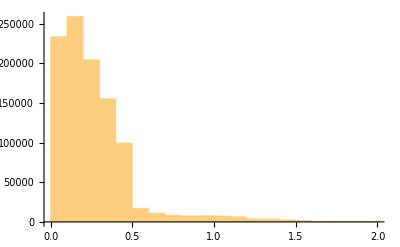

```mathematica
residuals=2 Abs[comparison[[;;,1]]-comparison[[;;,2]]]/Abs[comparison[[;;,1]]+comparison[[;;,2]]];
Mean[residuals]
Variance[residuals]
Total[residuals]
Total[residuals^2]
{Min[residuals],Max[residuals]}
Histogram[residuals]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
data=ReadList["/home/cplumber/CausalChargeDiffusion/1F1.test",Number];
len=Length[data];
```

```mathematica
ar=data[[Range[1,len,8]]];
ai=data[[Range[2,len,8]]];
br=data[[Range[3,len,8]]];
bi=data[[Range[4,len,8]]];
zr=data[[Range[5,len,8]]];
zi=data[[Range[6,len,8]]];
resRE=data[[Range[7,len,8]]];
resIM=data[[Range[8,len,8]]];
```

```mathematica
comparison=Table[{resRE[[i]]+I resIM[[i]],Hypergeometric1F1[ar[[i]]+I ai[[i]],br[[i]]+I bi[[i]],zr[[i]]+I zi[[i]]]},{i,Length[ar]}];
```

1.46143×10^-11

1.93523×10^-22

0.0000301113

8.3879×10^-16

{0.,8.68829×10^-11}

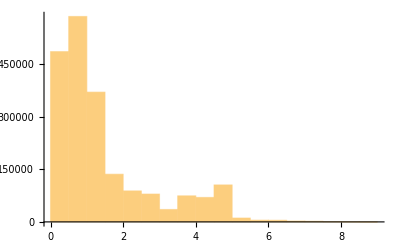

```mathematica
residuals=2 Abs[comparison[[;;,1]]-comparison[[;;,2]]]/Abs[comparison[[;;,1]]+comparison[[;;,2]]];
Mean[residuals]
Variance[residuals]
Total[residuals]
Total[residuals^2]
{Min[residuals],Max[residuals]}
Histogram[residuals]
```